```mathematica
a={1,2,3,4}
z={{1,2},{a,b}}
a[[2]]
```

{1,2,3,4}

{{1,2},{{1,2,3,4},b}}

2

```mathematica
z[[2,1]]
```

{1,2,3,4}

```mathematica
Part[a,{2,3,4}]
```

{2,3,4}

```mathematica
x=(c=11;d=3 ;c d)
```

33

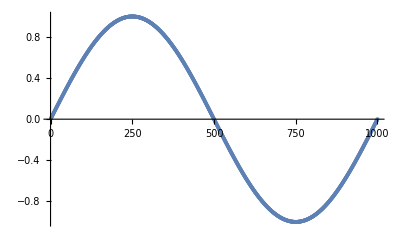

```mathematica
nmax=1000;
s=Table[Sin[2 Pi n/nmax],{n,nmax}]//N;
ListPlot[s]
```

```mathematica
Clear[x]
```

```mathematica
nmax=10;
λ=2;
x0=0.01;
x=Table[0,{n,nmax}];
x[[1]]=x0;
x=Table[λ (1-x[[n-1]])  x[[n-1]],{n,2,nmax}]
```

{0.0198,0,0,0,0,0,0,0,0}

```mathematica
(* tutaj eksperymenty *)
```

```mathematica
rob=Table[λ (1-x[[n-1]])  x[[n-1]],{n,2,nmax}]
```

```mathematica
(* koniec eksperymentow *)
```

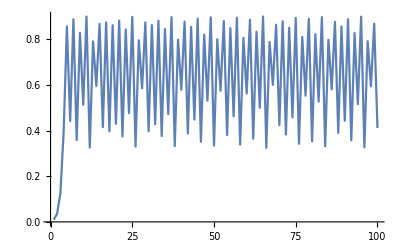

```mathematica
nmax=100;
λ=3.6;
x0=0.01;
x=Table[0,{n,nmax}];
x[[1]]=x0;
For[n=2,n<=nmax,n++,x[[n]]=λ (1-x[[n-1]]) x[[n-1]]]
ListPlot[x,Joined->True]
```

```mathematica
Manipulate[
x=Table[0,{n,nmax}];
x[[1]]=x0;
For[n=2,n≤nmax,n++,x[[n]]=λ (1-x[[n-1]]) x[[n-1]]]
ListPlot[x,Joined->True,PlotRange->All,ImageSize->Large],{nmax,1,100,1},{x0,0,1},{λ,1,4}]
```